```mathematica
Iin={{16360,0.03917},{16630,0.5113},{16913,1.0413},{17270,1.6896},{17595,2.277}};
IDCin={{16306,0.039-0.039},{16670,0.63-0.039},{17013,1.22-0.039},{17357,1.81-0.039},{17705,2.39-0.039}};IOUT={{16879,1},{17435,2.0},{17995,3},{18555,4}};
Vin = {{22073,22},{23075,23},{24086,24},{25091,25},{26094,26}};
Vout = {{3587,3.5985},{8111,8.1043},{11127,11.1089},{20187,20.121},{25246,25.160}};
```

```mathematica
FindFit[Vin,a*x+b,{a,b},x]
```

{a→0.000994232,b→0.0551241}

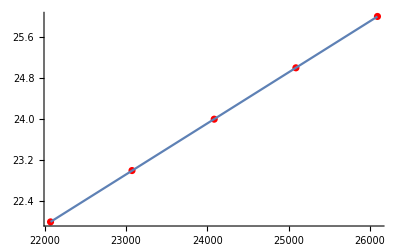

```mathematica
Show[ListPlot[Vin,PlotStyle->Red],Plot[a x+b/.{a->0.000994231637664585,b->0.05512408481367621},{x,22073,26094}]]
```

```mathematica
FindFit[Vout,a*x+b,{a,b},x]
```

{a→0.000995368,b→0.0301716}

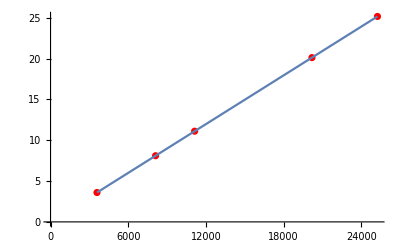

```mathematica
Show[ListPlot[Vout,PlotStyle->Red],Plot[a x+b/.{a->0.000995368190188952,b->0.030171614816503788},{x,3587,25246}]]
```

```mathematica
FindFit[Iin,a*x+b,{a,b},x]
```

{a→0.0018182,b→-29.7134}

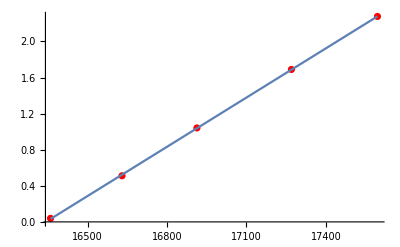

```mathematica
Show[ListPlot[Iin,PlotStyle->Red],Plot[a x+b/.{a->0.0018182017898451214,b->-29.713391864318254},{x,16360,17595}]]
```

```mathematica
FindFit[IDCin,a*x+b,{a,b},x]
```

{a→0.00168764,b→-27.5283}

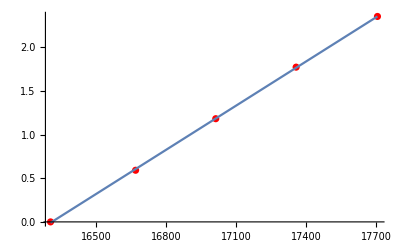

```mathematica
Show[ListPlot[IDCin,PlotStyle->Red],Plot[a x+b/.{a->0.0016876395247784762,b->-27.528285844386826},{x,16306,17705}]]
```

```mathematica
FindFit[IOUT,a*x+b,{a,b},x]
```

{a→0.00178954,b→-29.2036}

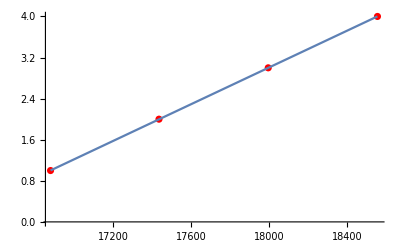

```mathematica
Show[ListPlot[IOUT,PlotStyle->Red],Plot[a x+b/.{a->0.0017895435318953875,b->-29.20355321105869},{x,16879,18555}]]
```